```mathematica
dat0=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/cos_test.dat"]//Flatten;
len=dat0//Length;
korak=2*Pi/(len-1);
xval=Table[-Pi+korak*i,{i,0,len-1}];
exactCos=Table[{xval[[i]],Cos[xval[[i]]]},{i,0,xval//Length}];
diff=Table[{xval[[i]],Cos[xval[[i]]] - dat0[[i]]},{i,0,xval//Length}];
```

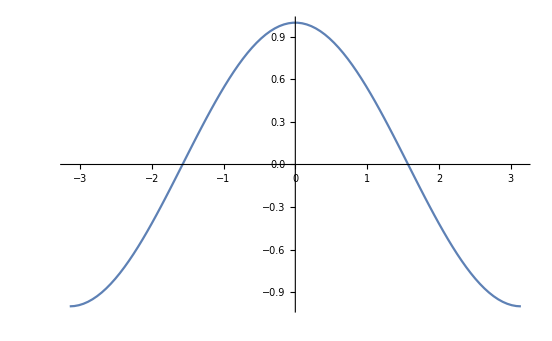

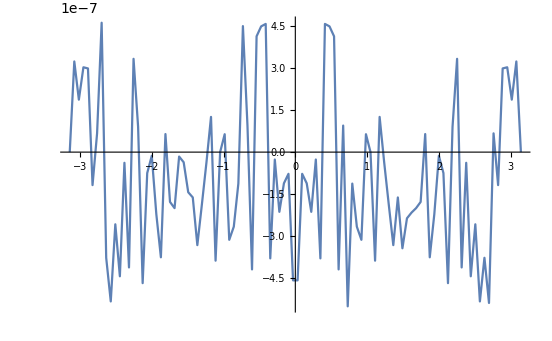

```mathematica
ListLinePlot[{
Transpose[{xval,dat0}]}]
ListLinePlot[diff]
```

```mathematica
dat0=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/sin_test.dat"]//Flatten;
len=dat0//Length;
korak=2*Pi/(len-1);
xval=Table[-Pi+korak*i,{i,0,len-1}];
exactCos=Table[{xval[[i]],Sin[xval[[i]]]},{i,0,xval//Length}];
diff=Table[{xval[[i]],Sin[xval[[i]]] - dat0[[i]]},{i,0,xval//Length}];
```

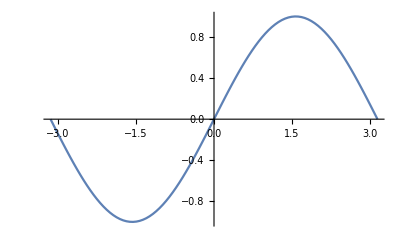

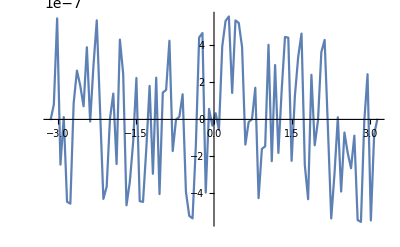

```mathematica
ListLinePlot[{
Transpose[{xval,dat0}]}]
ListLinePlot[diff]
```

```mathematica
dat0=Import["/home/jure/Documents/opengl_ucenje/geometrical_objects/testing/data/cos_test.dat"]//Flatten;
len=dat0//Length;
korak=2*Pi/(len-1);
xval=Table[-Pi+korak*i,{i,0,len-1}];
exactCos=Table[{xval[[i]],Cos[xval[[i]]]},{i,0,xval//Length}];
diff=Table[{xval[[i]],Cos[xval[[i]]] - dat0[[i]]},{i,0,xval//Length}];
```

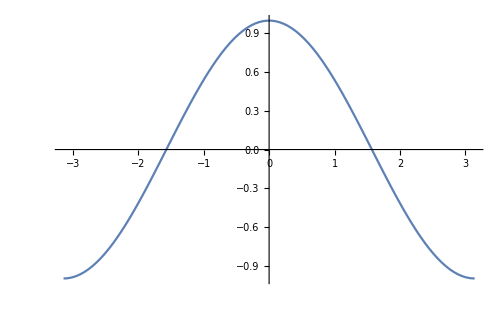

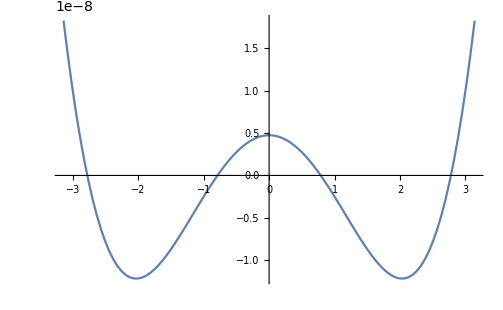

```mathematica
ListLinePlot[{
Transpose[{xval,dat0}]}]
ListLinePlot[diff]
```

```mathematica
coeff=Table[2/Pi*NIntegrate[Cos[Pi*Cos[theta]]*Cos[m*theta],{theta, 0,Pi}, WorkingPrecision->40,AccuracyGoal->40, MaxRecursion->1000],{m,0,26,2}];
coeff[[1]]=coeff[[1]]/2;
coeff
```

{-0.3042421776440938642020349128177049239697,-0.9708678652630182194109914323663784757039,0.3028491552626994215074191186309676140775,-0.02909193396501112114732073920800360778849,0.001392243991176231859984622208952274539411,-0.00004018994451075494298816526236368837878949,7.782767011815306088573057896947073998291×10^-7,-1.08265303418582848109342149267869577559×10^-8,1.135109177911507701030194019523024834037×10^-10,-9.295296632678756552885410084526215786661×10^-13,6.111364188334767723806229076684641965132×10^-15,-3.297657841343458986382435554107381460019×10^-17,1.486813423673207704795437109347570207022×10^-19,-5.685578136847164353761054026365713383437×10^-22}

```mathematica
coeff=Table[2/Pi*NIntegrate[Sin[Pi*Cos[theta]]*Cos[m*theta],{theta, 0,Pi}, WorkingPrecision->40,AccuracyGoal->40, MaxRecursion->1000],{m,1,31,2}];
coeff
```

{0.5692306863595055146906211993722628114196,-0.6669166724059790707804371634797734966045,0.1042823687342369494809202521862043939116,-0.006840633536991579009851374503285063910684,0.0002500068849503862276522158590075481730046,-5.850248308639143691717116193971950655104×10^-6,9.534772750299401140044067750300658462647×10^-8,-1.145638441709463151347564618146685930344×10^-9,1.057427261753912858869898216472797435085×10^-11,-7.735270995404307094156646286268862437722×10^-14,4.595956146182959459195691643430204238586×10^-16,-2.262305928197411104312660436182426308008×10^-18,9.377647799153135796251624441737014705742×10^-21,-3.318599491698564909515356552225801325484×10^-23,1.014380222196161580311718419311112037293×10^-25,-2.705193531668109420814186495894754642391×10^-28}

```mathematica
SetPrecision[ChebyshevT[5,{1.0,2.5,3.6,4.8}], 20]
```

{1.,1262.5,8759.4681600000003527,38580.794879999994009}